```mathematica
matrix = {{ℏ*ω*n +ϵ/2, g*Sqrt[n+1]},{g*Sqrt[n+1],ℏ*ω*(n+1) -ϵ/2}};
FullSimplify[Eigenvalues[matrix]]
FullSimplify[Eigenvectors[matrix]]
```

{1/2 (ω (ℏ+2 n ℏ)-√(4 g^2 (1+n)+(ϵ-ω ℏ)^2)),1/2 (ω (ℏ+2 n ℏ)+√(4 g^2 (1+n)+(ϵ-ω ℏ)^2))}

{{(ϵ-ω ℏ-√(4 g^2 (1+n)+(ϵ-ω ℏ)^2))/(2 g √(1+n)),1},{(ϵ-ω ℏ+√(4 g^2 (1+n)+(ϵ-ω ℏ)^2))/(2 g √(1+n)),1}}

```mathematica
(* g = g/(ℏω), e = ϵ/(ℏω) *)
```

```mathematica
(* energynplus is E_n,+ / (ℏω) *)
```

```mathematica
energynplus[g_,n_,e_] := 1/2*((2n+1)+Sqrt[4*g^2*(n+1)+(e-1)^2]);
energynminus[g_,n_,e_] := 1/2*((2n+1)-Sqrt[4*g^2*(n+1)+(e-1)^2]);
```

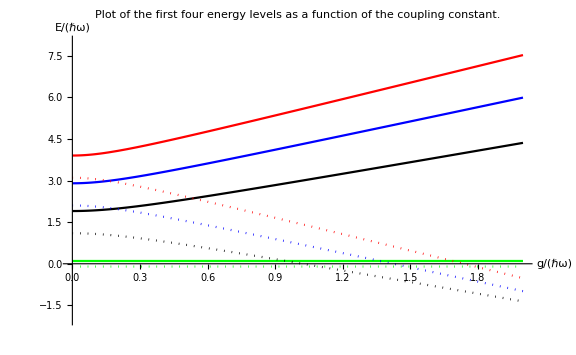

```mathematica
plot1plus = Plot[energynplus[g,1,0.2],{g,0,2},PlotRange ->{-1,5},PlotStyle->Black];
plot1minus = Plot[energynminus[g,1,0.2],{g,0,2},PlotStyle->{Black, Dotted}, PlotRange->{-7,10}];
plot2plus = Plot[energynplus[g,2,0.2],{g,0,2},PlotStyle->Blue];
plot2minus = Plot[energynminus[g,2,0.2],{g,0,2},PlotStyle->{Blue,Dotted}];
plot3plus = Plot[energynplus[g,3,0.2],{g,0,2},PlotStyle->Red];
plot3minus = Plot[energynminus[g,3,0.2],{g,0,2},PlotStyle->{Red,Dotted}];
plot0plus = Plot[0.1, {g,0,2},PlotStyle->Green];
plot0minus = Plot[-0.1, {g,0,2},PlotRange->{-2,8}, PlotStyle->{Green,Dotted}];
totalplot = Show[plot0minus, plot0plus,plot1minus,plot1plus,plot2minus,plot2plus,plot3minus,plot3plus, PlotLegends ->{"E_(0, -)","E_(0, +)","E_(1, -)","E_(1, +)","E_(2, -)","E_(2, +)","E_(3, -)","E_(3, +)"},PlotLabel->"Plot of the first four energy levels as a function of the coupling constant.", AxesLabel->{"g/(ℏω)", "E/(ℏω)"}, ImageSize->Large]
```

```mathematica
Solve[energynminus[g,1,e] == energynminus[g,2,e],g]
```

{{g→-√(5-√(25-2 e+e^2))},{g→√(5-√(25-2 e+e^2))},{g→-√(5+√(25-2 e+e^2))},{g→√(5+√(25-2 e+e^2))}}

```mathematica
photonN[g_,e_]:=Piecewise[{{0,g<1/(2*Sqrt[2])*Sqrt[(e+3)^2-(e-1)^2]},{(((e-1-Sqrt[8g^2+(e-1)^2])/(2*Sqrt[2]*g))^2+1)^(-1),g>1/(2*Sqrt[2])*Sqrt[(e+3)^2-(e-1)^2]}}];
```

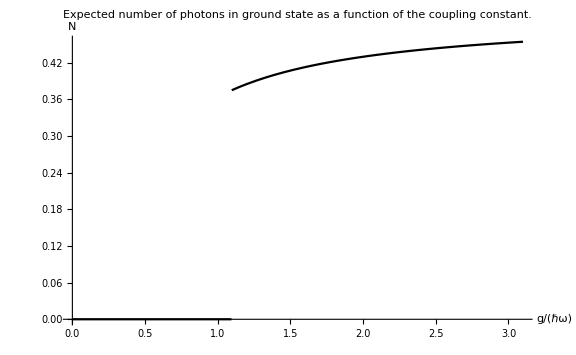

```mathematica
Plot[photonN[g,0.2],{g,0,3.1},PlotStyle->Black, AxesLabel->{"g/(ℏω)","N"},PlotLabel->"Expected number of photons in ground state as a function of the coupling constant.", ImageSize->Large]
```

```mathematica
transitionRate[e_] := 2Pi/(e-1)^2;
```

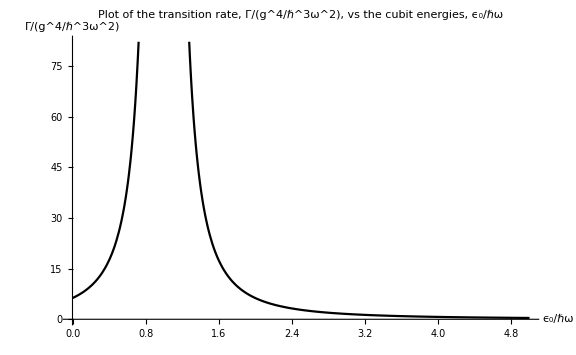

```mathematica
Plot[transitionRate[e],{e,0,5},PlotStyle->Black,PlotLabel->"Plot of the transition rate, Γ/(g^4/ℏ^3ω^2), vs the cubit energies, ϵ_0/ℏω", AxesLabel->{"ϵ_0/ℏω","Γ/(g^4/ℏ^3ω^2)"},ImageSize->Large]
```